B1:
a)

```mathematica
VMorse[r_]:=depth*(Exp[-2*α*(r-dis)]-2*Exp[-α*(r-dis)]);
bab = 1.162;
bbc = 1.162;
VAB[r_] = VMorse[r]/.{depth-> 7.65, α-> 2.5, dis-> bab};
VBC[r_] = VMorse[r]/.{depth-> 7.65, α-> 2.5, dis-> bbc};
V[rAB_,rBC_] := VAB[rAB]+VBC[rBC];
kb = 8.617*10^(-5);
Et[T_]:= kb*T;
```

```mathematica
Series[V[rAB,rBC],{rAB,bab,2},{rBC,bbc,2}]
```

(-15.3+47.8125 (rBC-1.162)^2+O[rBC-1.162]^3)+47.8125 (rAB-1.162)^2+O[rAB-1.162]^3

b)

```mathematica
Series[VAB[r],{r,bab,2}]
```

```mathematica
HarmonicAB[r_]:= -7.56 + 47.8125 *(r - 1.162)^2
```

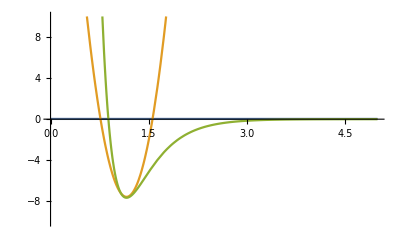

```mathematica
Plot[{Et[293],HarmonicAB[r],VAB[r]}, {r,0,5},PlotRange-> {-10,10}]
```

C) Using  V =1/2Kx^2  and looking at the series expansion above , It can be concluded that K = 2(47.8125). 
K = 95.625.

D)

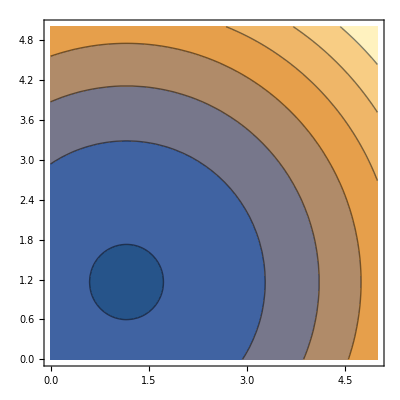

```mathematica
HarmonABC[rAB_,rBC_]:= -15.3+47.8125((rBC-bbc)^2+(rAB-bab)^2)
ContourPlot[HarmonABC[rAB,rBC],{rAB,0,5},{rBC,0,5}]
```

Compared to the Plot from part A, one can state that this plot is slower and more circumscribed then the other plot.

E)

```mathematica
FAB[rAB_]= D[VAB[rAB],rAB];
FBC[rBC_]= D[VBC[rBC],rBC];
F[rAB_,rBC_]:= {FAB[rAB],FBC[rBC]-FAB[rAB],-FBC[rBC]}
F[bab,bbc]
dx = 0.01;
MatrixMODE = {
-(F[bab-dx,bbc]-F[bab+dx,bbc])/(2dx),
-(F[bab+dx,bbc-dx]-F[bab-dx,bbc+dx])/(2dx),
-(F[bab,bbc+dx]-F[bab,bbc-dx])/(2dx)};
MatrixMODE //MatrixForm
```

(95.6947 | -95.6947 | 0.
-95.6947 | 191.389 | -95.6947
0. | -95.6947 | 95.6947)

```mathematica
Eigenvalues[MatrixMODE]
Eigenvectors[MatrixMODE] //MatrixForm
```

{287.084,95.6947,8.43885×10^-15}

(-0.408248 | 0.816497 | -0.408248
-0.707107 | 1.05007×10^-15 | 0.707107
0.57735 | 0.57735 | 0.57735)

The Eigen Vectors of this system is represented above in the 3x3 matrix form, while the Eigenvalues are in a 1x3 matrix. Each row of the matrix above represents a normal mode of motion. The first row models A and C the oxygen molecules moving to the left while the carbon  atom (B) moves to the right. Therefore this is an asymmetric stretch. While the second row shows similar features except for the fact that atom B(carbon ) stays in the same location as atom A and C move in opposite directions at equal magnitudes.Therefore this represents the symmetric stretch. The third row represents a translation since all of the atoms are moving in the same direction.
The frequencies for asymmetric and symmetric stretching are found in the eigen-value matrix above where asymmetric frequency is 287.084, and symmetric frequencies is 95.6947.

f) Looking at the frequency modes in this part , we see that they are the same as the frequencies obtained in the simulation from part A (After dimensional analysis and conversions are done).

g) The zero point energy is calculated by the following equation E = hV ==  95.69*h == -401.433eV

h)

```mathematica
maaassq=2;
mbbbssq=12;
mcccssq=2;
xAAffssq[0] = -bAB -0.02;
xBBffssq[0] = 0;
xCCffssq[0] = bBC + 0.02;
vAAffssq[0] = 0;
vBBffssq[0] = 0;
vCCffssq[0] = 0;
divABBffssq[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCffssq[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaffssq[0] = divABBffssq[xBBffssq[0] - xAAffssq[0],xCCffssq[0]-xBBffssq[0]];
fbbffssq[0] = -divABBffssq[xBBffssq[0] - xAAffssq[0],xCCffssq[0]-xBBffssq[0]] + divABBffssq[xBBffssq[0]-xAAffssq[0],xCCffssq[0]-xBBffssq[0]];
fccffssq[0] = -divBCCffssq[xBBffssq[0]-xAAffssq[0],xCCffssq[0]-xBBffssq[0]];
```

```mathematica
time = 30.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAffssq[n+1] = xAAffssq[n] + dt*vAAffssq[n] + 1/2*faaffssq[n]/maaassq *dt^2;
xBBffssq[n+1] = xBBffssq[n] + dt*vBBffssq[n]+1/2 *fbbffssq[n]/mbbbssq *dt^2;
xCCffssq[n+1] = xCCffssq[n] + dt*vCCffssq[n]+1/2 *fccffssq[n]/mcccssq*dt^2;
faaffssq[n + 1] = divABBffssq[xBBffssq[n + 1] - xAAffssq[n + 1],xCCffssq[n + 1]-xBBffssq[n + 1]];
fbbffssq[n + 1] = -divABBffssq[xBBffssq[n + 1 ] - xAAffssq[n + 1],xCCffssq[n + 1]-xBBffssq[n + 1]] + divABBffssq[xBBffssq[n + 1]-xAAffssq[n+1],xCCffssq[n + 1]-xBBffssq[n + 1]];
fccffssq[n + 1] = -divBCCffssq[xBBffssq[n + 1]-xAAffssq[0],xCCffssq[n + 1]-xBBffssq[n + 1]];
vAAffssq[n+1] = vAAffssq[n] + dt/(2*maaassq)*(faaffssq[n] + faaffssq[n+1]);
vBBffssq[n+1] = vBBffssq[n] + dt/(2*mbbbssq)*(fbbffssq[n] + fbbffssq[n+1]);
vCCffssq[n+1] = vCCffssq[n] + dt/(2*mcccssq)*(fccffssq[n] + fccffssq[n+1]),
{n,0,nSteps}]
rData = Table[{xBBffssq[n]-xAAffssq[n],xCCffssq[n]-xBBffssq[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAffssq[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAffssq[n]},{n,0,nSteps}];
ListPlot[rData,PlotStyle -> Blue]
Animate[ListPlot[{{xAAffssq[n],0},{xBBffssq[n],0},{xCCffssq[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

```mathematica
maaassq=2;
mbbbssq=0;
mcccssq=10;
xAAffssq[0] = -bAB -0.02;
xBBffssq[0] = 0;
xCCffssq[0] = bBC + 0.02;
vAAffssq[0] = 0;
vBBffssq[0] = 0;
vCCffssq[0] = 0;
divABBffssq[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCffssq[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaffssq[0] = divABBffssq[xBBffssq[0] - xAAffssq[0],xCCffssq[0]-xBBffssq[0]];
fbbffssq[0] = -divABBffssq[xBBffssq[0] - xAAffssq[0],xCCffssq[0]-xBBffssq[0]] + divABBffssq[xBBffssq[0]-xAAffssq[0],xCCffssq[0]-xBBffssq[0]];
fccffssq[0] = -divBCCffssq[xBBffssq[0]-xAAffssq[0],xCCffssq[0]-xBBffssq[0]];
```

```mathematica
time = 30.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAffssq[n+1] = xAAffssq[n] + dt*vAAffssq[n] + 1/2*faaffssq[n]/maaassq *dt^2;
xBBffssq[n+1] = xBBffssq[n] + dt*vBBffssq[n]+1/2 *fbbffssq[n]/mbbbssq *dt^2;
xCCffssq[n+1] = xCCffssq[n] + dt*vCCffssq[n]+1/2 *fccffssq[n]/mcccssq*dt^2;
faaffssq[n + 1] = divABBffssq[xBBffssq[n + 1] - xAAffssq[n + 1],xCCffssq[n + 1]-xBBffssq[n + 1]];
fbbffssq[n + 1] = -divABBffssq[xBBffssq[n + 1 ] - xAAffssq[n + 1],xCCffssq[n + 1]-xBBffssq[n + 1]] + divABBffssq[xBBffssq[n + 1]-xAAffssq[n+1],xCCffssq[n + 1]-xBBffssq[n + 1]];
fccffssq[n + 1] = -divBCCffssq[xBBffssq[n + 1]-xAAffssq[0],xCCffssq[n + 1]-xBBffssq[n + 1]];
vAAffssq[n+1] = vAAffssq[n] + dt/(2*maaassq)*(faaffssq[n] + faaffssq[n+1]);
vBBffssq[n+1] = vBBffssq[n] + dt/(2*mbbbssq)*(fbbffssq[n] + fbbffssq[n+1]);
vCCffssq[n+1] = vCCffssq[n] + dt/(2*mcccssq)*(fccffssq[n] + fccffssq[n+1]),
{n,0,nSteps}]
rData = Table[{xBBffssq[n]-xAAffssq[n],xCCffssq[n]-xBBffssq[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAffssq[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAffssq[n]},{n,0,nSteps}];
ListPlot[rData,PlotStyle -> Blue]
Animate[ListPlot[{{xAAffssq[n],0},{xBBffssq[n],0},{xCCffssq[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

i) The asymmetric stretch does not follow a good harmonic approximation since the anharmonicity of the atoms and the distance within the bounds cannot be confound by the harmonic potential approximation model with a contour plot.

j)

```mathematica
maaassqq=2;
mbbbssqq=0;
mcccssqq=10;
xAAffssqq[0] = -1.624 -0.02;
xBBffssqq[0] = 5;
xCCffssqq[0] = 1.245 + 0.02;
vAAffssqq[0] = 0;
vBBffssqq[0] = 0;
vCCffssqq[0] = 0;
divABBffssqq[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCffssqq[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaffssqq[0] = divABBffssqq[xBBffssqq[0] - xAAffssqq[0],xCCffssqq[0]-xBBffssqq[0]];
fbbffssqq[0] = -divABBffssqq[xBBffssqq[0] - xAAffssqq[0],xCCffssqq[0]-xBBffssqq[0]] + divABBffssqq[xBBffssqq[0]-xAAffssqq[0],xCCffssqq[0]-xBBffssqq[0]];
fccffssqq[0] = -divBCCffssqq[xBBffssqq[0]-xAAffssqq[0],xCCffssqq[0]-xBBffssqq[0]];
time = 30.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAffssqq[n+1] = xAAffssqq[n] + dt*vAAffssqq[n] + 1/2*faaffssqq[n]/maaassqq *dt^2;
xBBffssqq[n+1] = xBBffssqq[n] + dt*vBBffssqq[n]+1/2 *fbbffssqq[n]/mbbbssqq *dt^2;
xCCffssqq[n+1] = xCCffssqq[n] + dt*vCCffssqq[n]+1/2 *fccffssqq[n]/mcccssqq*dt^2;
faaffssqq[n + 1] = divABBffssqq[xBBffssqq[n + 1] - xAAffssqq[n + 1],xCCffssqq[n + 1]-xBBffssqq[n + 1]];
fbbffssqq[n + 1] = -divABBffssqq[xBBffssqq[n + 1 ] - xAAffssqq[n + 1],xCCffssqq[n + 1]-xBBffssqq[n + 1]] + divABBffssqq[xBBffssqq[n + 1]-xAAffssqq[n+1],xCCffssqq[n + 1]-xBBffssqq[n + 1]];
fccffssqq[n + 1] = -divBCCffssqq[xBBffssqq[n + 1]-xAAffssqq[0],xCCffssqq[n + 1]-xBBffssqq[n + 1]];
vAAffssqq[n+1] = vAAffssqq[n] + dt/(2*maaassqq)*(faaffssqq[n] + faaffssqq[n+1]);
vBBffssqq[n+1] = vBBffssqq[n] + dt/(2*mbbbssqq)*(fbbffssqq[n] + fbbffssqq[n+1]);
vCCffssqq[n+1] = vCCffssqq[n] + dt/(2*mcccssqq)*(fccffssqq[n] + fccffssqq[n+1]),
{n,0,nSteps}]
rData = Table[{xBBffssqq[n]-xAAffssqq[n],xCCffssqq[n]-xBBffssqq[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAffssqq[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAffssqq[n]},{n,0,nSteps}];
ListPlot[rData,PlotStyle -> Blue]
Animate[ListPlot[{{xAAffssqq[n],0},{xBBffssqq[n],0},{xCCffssqq[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
frData=Abs[Fourier[Vrdata]];
fData=Table[{2 Pi/time(n-1),frData[[n]]},{n,1,nSteps}];
ListPlot[fData,PlotRange->{{0,40},All}, Joined->True]
```

Having atoms with three different atoms at different spring constants would eliminate any symmetric stretching and symmetry due to different spring constants. The size of the atoms would also impact the symmetry since the force of the atom is dependent on the mass of that atom.